# Midpoint Ellipse Algorithm

```mathematica
FourWaySymmetry[pixelList_] := Module[{n = Length[pixelList], i, newPixelList = {}, x, y},
	For[i = 1, i <= n, i++,
		{x, y} = pixelList[[i]];
		AppendTo[newPixelList, {x, y}];
		AppendTo[newPixelList, {x, -y}];
		AppendTo[newPixelList, {-x, y}];
		AppendTo[newPixelList, {-x, -y}];
	];
	Return[newPixelList];
]
```

```mathematica
DrawEllipse[origin_, a_, b_] := Module[{h, d1, d2, x, y, pixelList={}},
	h = 4b^2 + a^2 (1 - 4b);
	d1 = 12 b^2;
	d2 = -8 a^2 (b - 1);
	
	{x, y} = {0, b};
	AppendTo[pixelList, {x, y} + origin];
	
	While[b^2 x < a^2 y,
		x = x + 1;
		If[h > 0,
			y = y - 1;
			h = h + d1 + d2;
			d2 = d2 + 8 a^2;
			,
			h = h + d1;
		];
		d1 = d1 + 8 b^2;
		AppendTo[pixelList, {x, y} + origin];
	
	];
	x = x + 1;
	While[y >= 0,
		y = y - 1;
		If[h > 0,
			h = h + d2;
			,
			x = x + 1;
			h = h + d1 + d2;
			d1 = d1 + 8 b^2;
		];
		d2 = d2 + 8 a^2;
		AppendTo[pixelList, {x, y} + origin];
		
	];
	pixelList = FourWaySymmetry[pixelList];
	Return[pixelList];
]
```

```mathematica
DrawPixel[pointList_] := Module[{},
	Return[Table[{Black,Rectangle[pointList[[i]], pointList[[i]] + {1,1}]},{i, Length[pointList]}]];
]
```

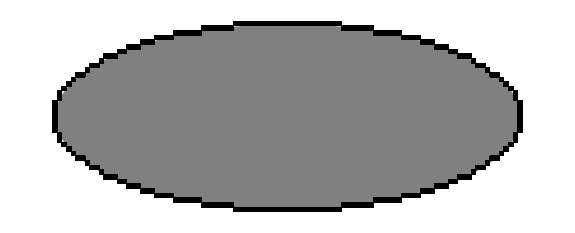

```mathematica
Show[
	Graphics[{Gray, Ellipsoid[{0.5, 0.5}, {50, 20}]}],
	Graphics[DrawPixel[DrawEllipse[{0,0}, 50, 20]]]
]
```